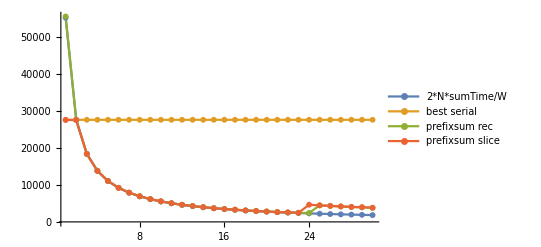

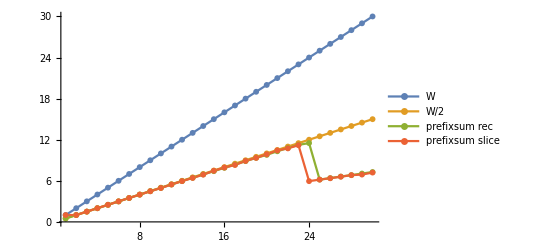

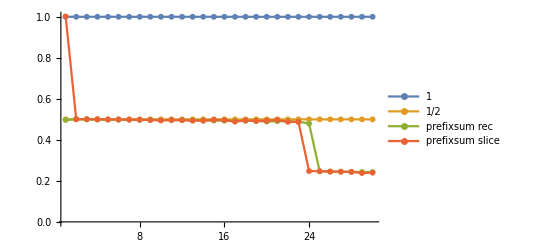

0.500909

0.490356

0.501177

0.487988

```mathematica
nameRec := "prefixsum rec"
nameSlice := "prefixsum slice" 
timesRec := {55487.11,27524.07,18352.71,13816.41,11061.25,9225.90,7905.47,6928.67,6152.84,5556.57,5049.71,4627.59,4279.83,3979.06,3720.53,3491.53,3300.22,3106.12,2949.06,2817.17,2672.90,2556.04,2451.18,2396.07,4463.65,4311.76,4163.30,4036.06,3906.79,3785.95}
timesSlice := {27528.15,27509.37,18359.21,13767.53,11047.35,9201.53,7896.21,6923.95,6168.90,5574.06,5049.04,4631.92,4296.36,3993.56,3694.85,3475.20,3316.63,3097.91,2950.41,2795.57,2642.07,2568.44,2461.29,4634.28,4465.48,4326.80,4178.15,4039.63,3990.18,3828.34}
best1 := 27574.11

idealTime[w_] := 2*best1/w
idealTimes := Map[idealTime, Range[30]]
ListLinePlot[{idealTimes, ConstantArray[best1, 30], timesRec, timesSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"2*N*sumTime/W", "best serial", nameRec, nameSlice}]

speedupFunc[x_] := best1/ x
speedupRec := Map[speedupFunc, timesRec]
speedupSlice := Map[speedupFunc, timesSlice]
ListLinePlot[{Range[30], Range[0.5, 15, 0.5], speedupRec, speedupSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"W", "W/2", nameRec, nameSlice}]

efficFuncRec[x_] := speedupRec[[x]]/ x
efficFuncSlice[x_] := speedupSlice[[x]]/ x
efficRec := Map[efficFuncRec, Range[30]]
efficSlice := Map[efficFuncSlice, Range[30]]
ListLinePlot[{ConstantArray[1, 30], ConstantArray[0.5, 30], efficRec, efficSlice}, PlotRange -> All, PlotMarkers ->{{●, 6}, {●, 6}, {●, 6}, {●, 6}}, PlotLegends -> {"1", "1/2", nameRec, nameSlice}]

Print[efficRec[[2]]]
Print[efficRec[[22]]]
Print[efficSlice[[2]]]
Print[efficSlice[[22]]]
```